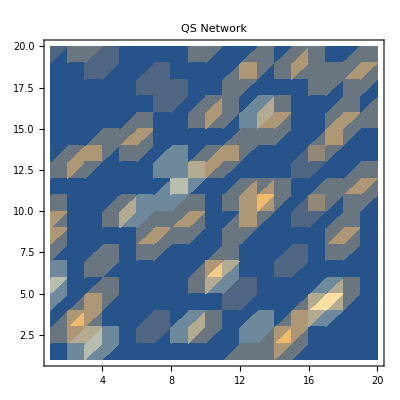

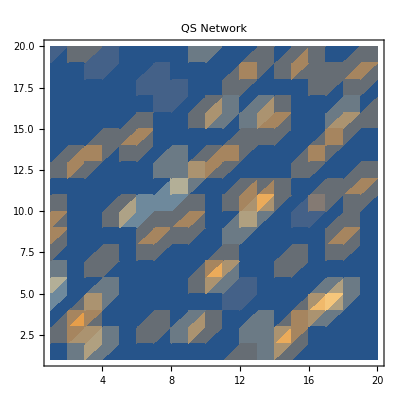

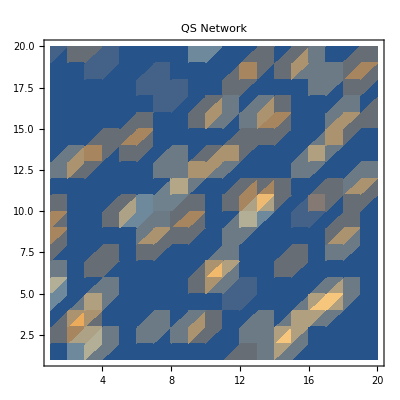

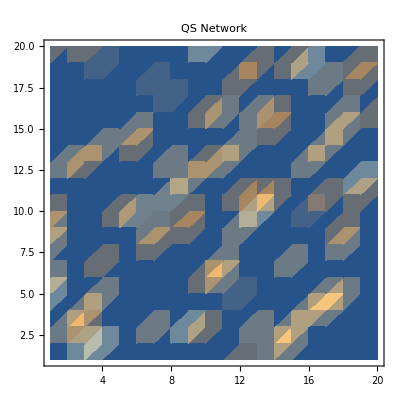

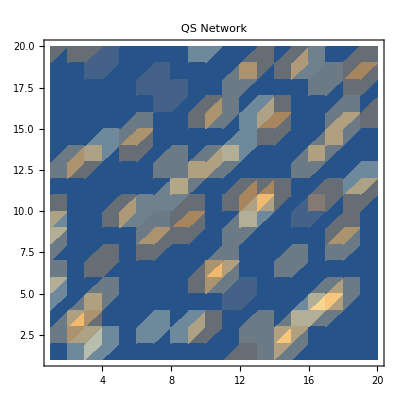

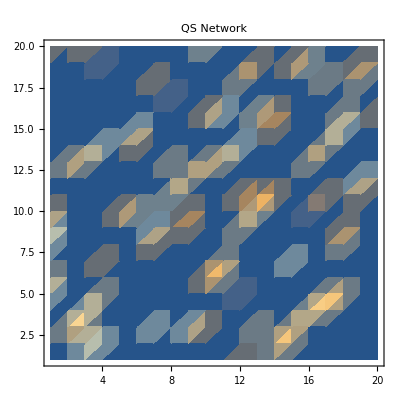

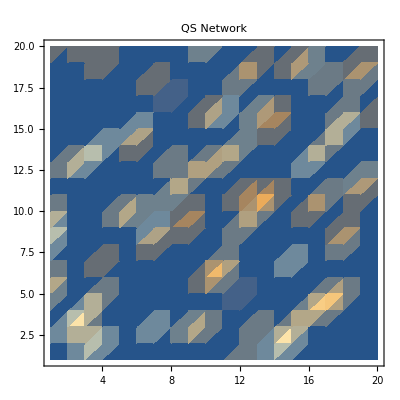

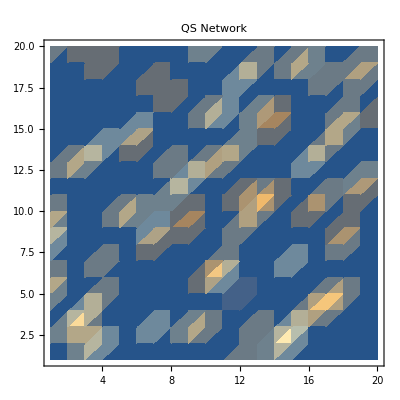

```mathematica
areaSize=20;
cellDensity=0.2;
observationTime=100;
timeforSignaling=1;

cellDistribution[]:=HalfNormalDistribution[0.5];

(*Auxiliary signalling functions*)
neigh={};
For[k=1,k≤15,k++,
neighborhood=Table[Max[0,k-Abs[x]-Abs[y]],{x,-5,5},{y,-5,5}];
neigh=Append[neigh,neighborhood]]; 

aiDomain={1,2,3,4,5,6,7,8,9,10};

aiConcentration[level_]:=Switch[level,1,neigh[[3]],2,neigh[[5]],3,neigh[[7]],4,neigh[[9]],5,neigh[[8]],6,neigh[[7]],7,neigh[[6]],8,neigh[[5]],9,neigh[[4]],10,neigh[[3]]];

aiCell[level_]:=Switch[level,1,1,2,3,3,5,4,7,5,6,6,5,7,4,8,3,9,2,10,1];

aiDistance[level_]:=1+aiCell[level];

aiUpdate[levels_,lccore_]:=(levelsNew=levels;
cellPos1=Position[levels[[First[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]>First[aiDomain]+3,levelsNew[[First[aiDomain]+1]]=ReplacePart[levelsNew[[First[aiDomain]+1]],1,cellPos1[[s]]];levelsNew[[First[aiDomain]]]=ReplacePart[levelsNew[[First[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
cellPos1=Position[levels[[Last[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]<Last[aiDomain]+3,levelsNew[[Last[aiDomain]-1]]=ReplacePart[levelsNew[[Last[aiDomain]-1]],1,cellPos1[[s]]];
levelsNew[[Last[aiDomain]]]=ReplacePart[levelsNew[[Last[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
For[r=First[aiDomain]+1,r<Last[aiDomain],r++,
cellPos1=Position[levels[[r]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,
If[conc1[[s]]<r+3,levelsNew[[r-1]]=ReplacePart[levelsNew[[r-1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]],If[conc1[[s]]>r+3,levelsNew[[r+1]]=ReplacePart[levelsNew[[r+1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]]];];];
];
Clear[cellPos1,conc1];
levelsNew
);

(*Initializing all necessary data structures*)
levels=Table[0,{Last[aiDomain]-First[aiDomain]+1},{areaSize},{areaSize}];
levelsDynamic=levels;
levelsDynamicNew=levels;
levelsStatic=levels;
graph=Range[observationTime];
productionList=Range[observationTime];
cells={{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0},{0,1,1,0,0,0,1,0,1,1,0,0,1,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0},{1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,0},{1,0,0,0,1,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0},{0,1,1,0,0,0,0,1,0,1,1,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0},{1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}; (*Changed*)
levels=ReplacePart[levels,cells,1];
lc=ListCorrelate[aiConcentration[1],cells,{-1,1},0];
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
levels=aiUpdate[levels,lccore];

nCells=Count[cells,1,2];
cellPos=Position[cells,1];
EdgeMatrix=Table[0,{nCells},{nCells}];

(*Main QS cycle*)
For[clock=1,clock≤observationTime,clock++,
(*update level and concentration table*)
If[Mod[clock,timeforSignaling]==0,
lc=Plus@@Function[{i},ListCorrelate[aiConcentration[i],levels[[i]],{-1,1},0]]/@aiDomain;
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
signalingCells=cells; 
For[k=1,k≤nCells,k++,
(*To avoid artificial cyclic activation-inhibition dependencies, only a small fraction of cells is signalling at once*)
If[Random[]<.8,signalingCells=ReplacePart[signalingCells,0,cellPos[[k]]]];
];
For[k=First[aiDomain],k≤Last[aiDomain],k++,
levelsStatic[[k]]=levels[[k]]-signalingCells;
mins=Position[levelsStatic[[k]],-1];
For[v=1,v≤Length[mins],v++,levelsStatic[[k]]=ReplacePart[levelsStatic[[k]],0,mins[[v]]]];
];
levelsDynamic=levels-levelsStatic;



levelsDynamicNew=aiUpdate[levelsDynamic,lccore];
levels=levelsDynamicNew+levelsStatic;

If[ clock>61 && clock < 70, x=1;
plx25={8,16,17,18,20,28,32,33,41,47,49,53,57,58,63,69}; (*Random int from matlab, 50 number or 25% of ~200 cells*)
plx50={8,9,10,13,14,16,18,20,22,23,26,29,31,32,33,34,39,40,42,44,45,46,47,50,52,53,55,57,59,60,62,63,64,66,67,68,69,72,74,75};
plx10={61,23,64,12,41,49,57,31};
For[x=1,x≤8,x++, (*n/2*)
{a,b}=cellPos[[plx10[[x]],1;;2]];
levels[[1;;10,a,b]]=0; (*Varying results probably due to updating, changes only cloud*)
levels[[4,a,b]]=1;
];
];


];

graph[[clock]]=Plus@@Function[{i},aiDistance[i]*levels[[i]]]/@aiDomain;
Print[ListDensityPlot[graph[[clock]],PlotLabel->"QS Network"]];
productionList[[clock]]=N[Total[graph[[clock]],2]/nCells](*average ai production per cell*)
]; (*end main QS cycle*)

(*Pathway Analysis*)
EdgeMatrix=Table[0,{nCells},{nCells}];
highlyConnectedCells=Table[0,{nCells}];
nHighlyConnected=0;
For[k=1,k≤nCells,k++,
maxDist=graph[[1]][[cellPos[[k,1]],cellPos[[k,2]]]];
For[v=1,v≤nCells,v++,
If[k==v,Continue[]];
dist=Abs[cellPos[[k,1]]-cellPos[[v,1]]]+Abs[cellPos[[k,2]]-cellPos[[v,2]]];
If[dist≤maxDist,EdgeMatrix[[k,v]]++];];
];
totalEdgeMatrix=Total[EdgeMatrix,{2}];
For[k=1,k≤nCells,k++,
If[totalEdgeMatrix[[k]]>5,nHighlyConnected++;highlyConnectedCells[[k]]=1];
];


(* To plot all unconncected nodes across time*)
For[n=1,n ≤ 1,n++,
EdgeMatrix=Table[0,{nCells},{nCells}];
highlyConnectedCells=Table[0,{nCells}];
nHighlyConnected=0;
For[k=1,k≤nCells,k++,
maxDist=graph[[n]][[cellPos[[k,1]],cellPos[[k,2]]]];
For[v=1,v≤nCells,v++,
If[k==v,Continue[]];
dist=Abs[cellPos[[k,1]]-cellPos[[v,1]]]+Abs[cellPos[[k,2]]-cellPos[[v,2]]];
If[dist≤maxDist,EdgeMatrix[[k,v]]++];];
];
totalEdgeMatrix=Total[EdgeMatrix,{2}];

]
```

```mathematica
SetDirectory["C:\Users\Sl\Documents\Neu\Cell-cell communication {QS based}\Edge matrix 20x20 actual deleted nodes 05-25\Manipulated direct - neg fb set"]
For[fs=1,fs≤100,fs++,
EdgeMatrix=Table[0,{nCells},{nCells}];
highlyConnectedCells=Table[0,{nCells}];
nHighlyConnected=0;
For[k=1,k≤nCells,k++,
maxDist=graph[[fs]][[cellPos[[k,1]],cellPos[[k,2]]]];
For[v=1,v≤nCells,v++,
If[k==v,Continue[]];
dist=Abs[cellPos[[k,1]]-cellPos[[v,1]]]+Abs[cellPos[[k,2]]-cellPos[[v,2]]];
If[dist≤maxDist,EdgeMatrix[[k,v]]++];];
];
If[fs== 1,
Export["Edgematrix-sm-01.csv",EdgeMatrix,"CSV"]
];
If[fs== 2,
Export["Edgematrix-sm-02.csv",EdgeMatrix,"CSV"]
];
If[fs== 3,
Export["Edgematrix-sm-03.csv",EdgeMatrix,"CSV"]
];
If[fs== 4,
Export["Edgematrix-sm-04.csv",EdgeMatrix,"CSV"]
];
If[fs== 5,
Export["Edgematrix-sm-05.csv",EdgeMatrix,"CSV"]
];
If[fs== 6,
Export["Edgematrix-sm-06.csv",EdgeMatrix,"CSV"]
];
If[fs== 7,
Export["Edgematrix-sm-07.csv",EdgeMatrix,"CSV"]
];
If[fs== 8,
Export["Edgematrix-sm-08.csv",EdgeMatrix,"CSV"]
];
If[fs== 9,
Export["Edgematrix-sm-09.csv",EdgeMatrix,"CSV"]
];
If[fs== 10,
Export["Edgematrix-sm-10.csv",EdgeMatrix,"CSV"]
];
If[fs== 11,
Export["Edgematrix-sm-11.csv",EdgeMatrix,"CSV"]
];
If[fs== 12,
Export["Edgematrix-sm-12.csv",EdgeMatrix,"CSV"]
];
If[fs== 13,
Export["Edgematrix-sm-13.csv",EdgeMatrix,"CSV"]
];
If[fs== 14,
Export["Edgematrix-sm-14.csv",EdgeMatrix,"CSV"]
];
If[fs== 15,
Export["Edgematrix-sm-15.csv",EdgeMatrix,"CSV"]
];
If[fs== 16,
Export["Edgematrix-sm-16.csv",EdgeMatrix,"CSV"]
];
If[fs== 17,
Export["Edgematrix-sm-17.csv",EdgeMatrix,"CSV"]
];
If[fs== 18,
Export["Edgematrix-sm-18.csv",EdgeMatrix,"CSV"]
];
If[fs== 19,
Export["Edgematrix-sm-19.csv",EdgeMatrix,"CSV"]
];
If[fs== 20,
Export["Edgematrix-sm-20.csv",EdgeMatrix,"CSV"]
];
If[fs== 21,
Export["Edgematrix-sm-21.csv",EdgeMatrix,"CSV"]
];
If[fs== 22,
Export["Edgematrix-sm-22.csv",EdgeMatrix,"CSV"]
];
If[fs== 23,
Export["Edgematrix-sm-23.csv",EdgeMatrix,"CSV"]
];
If[fs== 24,
Export["Edgematrix-sm-24.csv",EdgeMatrix,"CSV"]
];
If[fs== 25,
Export["Edgematrix-sm-25.csv",EdgeMatrix,"CSV"]
];
If[fs== 26,
Export["Edgematrix-sm-26.csv",EdgeMatrix,"CSV"]
];
If[fs== 27,
Export["Edgematrix-sm-27.csv",EdgeMatrix,"CSV"]
];
If[fs== 28,
Export["Edgematrix-sm-28.csv",EdgeMatrix,"CSV"]
];
If[fs== 29,
Export["Edgematrix-sm-29.csv",EdgeMatrix,"CSV"]
];
If[fs== 30,
Export["Edgematrix-sm-30.csv",EdgeMatrix,"CSV"]
];
If[fs== 31,
Export["Edgematrix-sm-31.csv",EdgeMatrix,"CSV"]
];
If[fs== 32,
Export["Edgematrix-sm-32.csv",EdgeMatrix,"CSV"]
];
If[fs== 33,
Export["Edgematrix-sm-33.csv",EdgeMatrix,"CSV"]
];
If[fs== 34,
Export["Edgematrix-sm-34.csv",EdgeMatrix,"CSV"]
];
If[fs== 35,
Export["Edgematrix-sm-35.csv",EdgeMatrix,"CSV"]
];
If[fs== 36,
Export["Edgematrix-sm-36.csv",EdgeMatrix,"CSV"]
];
If[fs== 37,
Export["Edgematrix-sm-37.csv",EdgeMatrix,"CSV"]
];
If[fs== 38,
Export["Edgematrix-sm-38.csv",EdgeMatrix,"CSV"]
];
If[fs== 39,
Export["Edgematrix-sm-39.csv",EdgeMatrix,"CSV"]
];
If[fs== 40,
Export["Edgematrix-sm-40.csv",EdgeMatrix,"CSV"]
];
If[fs== 41,
Export["Edgematrix-sm-41.csv",EdgeMatrix,"CSV"]
];
If[fs== 42,
Export["Edgematrix-sm-42.csv",EdgeMatrix,"CSV"]
];
If[fs== 43,
Export["Edgematrix-sm-43.csv",EdgeMatrix,"CSV"]
];
If[fs== 44,
Export["Edgematrix-sm-44.csv",EdgeMatrix,"CSV"]
];
If[fs== 45,
Export["Edgematrix-sm-45.csv",EdgeMatrix,"CSV"]
];
If[fs== 46,
Export["Edgematrix-sm-46.csv",EdgeMatrix,"CSV"]
];
If[fs== 47,
Export["Edgematrix-sm-47.csv",EdgeMatrix,"CSV"]
];
If[fs== 48,
Export["Edgematrix-sm-48.csv",EdgeMatrix,"CSV"]
];
If[fs== 49,
Export["Edgematrix-sm-49.csv",EdgeMatrix,"CSV"]
];
If[fs== 50,
Export["Edgematrix-sm-50.csv",EdgeMatrix,"CSV"]
];
If[fs== 51,
Export["Edgematrix-sm-51.csv",EdgeMatrix,"CSV"]
];
If[fs== 52,
Export["Edgematrix-sm-52.csv",EdgeMatrix,"CSV"]
];
If[fs== 53,
Export["Edgematrix-sm-53.csv",EdgeMatrix,"CSV"]
];
If[fs== 54,
Export["Edgematrix-sm-54.csv",EdgeMatrix,"CSV"]
];
If[fs== 55,
Export["Edgematrix-sm-55.csv",EdgeMatrix,"CSV"]
];
If[fs== 56,
Export["Edgematrix-sm-56.csv",EdgeMatrix,"CSV"]
];
If[fs== 57,
Export["Edgematrix-sm-57.csv",EdgeMatrix,"CSV"]
];
If[fs== 58,
Export["Edgematrix-sm-58.csv",EdgeMatrix,"CSV"]
];
If[fs== 59,
Export["Edgematrix-sm-59.csv",EdgeMatrix,"CSV"]
];
If[fs== 60,
Export["Edgematrix-sm-60.csv",EdgeMatrix,"CSV"]
];
If[fs== 61,
Export["Edgematrix-sm-61.csv",EdgeMatrix,"CSV"]
];
If[fs== 62,
Export["Edgematrix-sm-62.csv",EdgeMatrix,"CSV"]
];
If[fs== 63,
Export["Edgematrix-sm-63.csv",EdgeMatrix,"CSV"]
];
If[fs== 64,
Export["Edgematrix-sm-64.csv",EdgeMatrix,"CSV"]
];
If[fs== 65,
Export["Edgematrix-sm-65.csv",EdgeMatrix,"CSV"]
];
If[fs== 66,
Export["Edgematrix-sm-66.csv",EdgeMatrix,"CSV"]
];
If[fs== 67,
Export["Edgematrix-sm-67.csv",EdgeMatrix,"CSV"]
];
If[fs== 68,
Export["Edgematrix-sm-68.csv",EdgeMatrix,"CSV"]
];
If[fs== 69,
Export["Edgematrix-sm-69.csv",EdgeMatrix,"CSV"]
];
If[fs== 70,
Export["Edgematrix-sm-70.csv",EdgeMatrix,"CSV"]
];
If[fs== 71,
Export["Edgematrix-sm-71.csv",EdgeMatrix,"CSV"]
];
If[fs== 72,
Export["Edgematrix-sm-72.csv",EdgeMatrix,"CSV"]
];
If[fs== 73,
Export["Edgematrix-sm-73.csv",EdgeMatrix,"CSV"]
];
If[fs== 74,
Export["Edgematrix-sm-74.csv",EdgeMatrix,"CSV"]
];
If[fs== 75,
Export["Edgematrix-sm-75.csv",EdgeMatrix,"CSV"]
];
If[fs== 76,
Export["Edgematrix-sm-76.csv",EdgeMatrix,"CSV"]
];
If[fs== 77,
Export["Edgematrix-sm-77.csv",EdgeMatrix,"CSV"]
];
If[fs== 78,
Export["Edgematrix-sm-78.csv",EdgeMatrix,"CSV"]
];
If[fs== 79,
Export["Edgematrix-sm-79.csv",EdgeMatrix,"CSV"]
];
If[fs== 80,
Export["Edgematrix-sm-80.csv",EdgeMatrix,"CSV"]
];
If[fs== 81,
Export["Edgematrix-sm-81.csv",EdgeMatrix,"CSV"]
];
If[fs== 82,
Export["Edgematrix-sm-82.csv",EdgeMatrix,"CSV"]
];
If[fs==83,
Export["Edgematrix-sm-83.csv",EdgeMatrix,"CSV"]
];
If[fs== 84,
Export["Edgematrix-sm-84.csv",EdgeMatrix,"CSV"]
];
If[fs== 85,
Export["Edgematrix-sm-85.csv",EdgeMatrix,"CSV"]
];
If[fs== 86,
Export["Edgematrix-sm-86.csv",EdgeMatrix,"CSV"]
];
If[fs== 87,
Export["Edgematrix-sm-87.csv",EdgeMatrix,"CSV"]
];
If[fs== 88,
Export["Edgematrix-sm-88.csv",EdgeMatrix,"CSV"]
];
If[fs== 89,
Export["Edgematrix-sm-89.csv",EdgeMatrix,"CSV"]
];
If[fs== 90,
Export["Edgematrix-sm-90.csv",EdgeMatrix,"CSV"]
];
If[fs== 91,
Export["Edgematrix-sm-91.csv",EdgeMatrix,"CSV"]
];
If[fs== 92,
Export["Edgematrix-sm-92.csv",EdgeMatrix,"CSV"]
];
If[fs== 93,
Export["Edgematrix-sm-93.csv",EdgeMatrix,"CSV"]
];
If[fs== 94,
Export["Edgematrix-sm-94.csv",EdgeMatrix,"CSV"]
];
If[fs== 95,
Export["Edgematrix-sm-95.csv",EdgeMatrix,"CSV"]
];
If[fs== 96,
Export["Edgematrix-sm-96.csv",EdgeMatrix,"CSV"]
];
If[fs== 97,
Export["Edgematrix-sm-97.csv",EdgeMatrix,"CSV"]
];
If[fs== 98,
Export["Edgematrix-sm-98.csv",EdgeMatrix,"CSV"]
];
If[fs== 99,
Export["Edgematrix-sm-99.csv",EdgeMatrix,"CSV"]
];
If[fs== 100,
Export["Edgematrix-sm-100.csv",EdgeMatrix,"CSV"]
];
];
```

C:\Users\Sl\Documents\Neu\Cell-cell communication {QS based}\Edge matrix 20x20 actual deleted nodes 05-25\Manipulated direct - neg fb set

```mathematica
Dimensions[graph]
```

{100,20,20}

```mathematica
Export["Signal-all",graph,"CSV"]
```

Signal-all

```mathematica
graph1=ArrayReshape[graph,{100,400}]
```

{1}
 |  |  |  |

```mathematica
Dimensions[graph1]
```

{100,400}

```mathematica
Export["Signal-all",graph1,"CSV"]
```

Signal-all

```mathematica
Export["Signal-all.csv",graph1,"CSV"]
```

Signal-all.csv

```mathematica
graph[[1,1;;20,1;;20]]
```

{{0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0},{0,0,6,6,0,0,0,0,0,0,0,0,0,4,4,0,0,0,0,0},{0,4,4,0,0,0,2,0,6,4,0,0,6,0,4,0,0,0,0,0},{0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,4,6,0,0,0},{6,0,0,4,0,0,0,0,0,0,0,2,0,0,0,0,6,4,0,0},{6,0,0,0,0,0,0,0,0,4,6,0,0,0,0,0,0,0,0,0},{0,0,0,4,0,0,0,0,0,0,4,0,0,0,2,0,0,0,0,0},{4,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,4,0,0},{4,0,0,0,0,0,4,0,4,0,0,4,0,0,0,0,0,4,0,0},{4,0,0,0,4,6,0,0,4,0,0,0,4,0,0,2,0,0,0,0},{0,0,0,0,0,0,0,6,0,0,0,4,4,4,0,0,4,0,4,0},{0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,4,0},{0,4,4,0,0,0,0,6,0,4,4,0,0,0,0,2,0,0,0,0},{0,0,0,4,0,4,0,0,0,0,0,4,0,0,0,0,4,0,0,0},{0,0,0,0,0,4,0,0,0,0,0,0,0,4,0,0,0,4,0,0},{0,0,0,0,0,0,0,0,0,4,4,0,6,4,0,0,0,4,0,4},{0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,0,0,0,0,4,0,0,0,0,4,0,4,0},{0,0,0,2,0,0,0,0,0,0,0,0,4,0,4,4,0,0,4,0},{2,0,4,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0}}